## Datos v2 Phoenix 20-40%

```mathematica
v2P2040={{0.50,0.0964,0.0125,-0.00113,0.0133,-0.0113},{0.70,0.0668,0.0173,-0.0289,0.0336,-0.0485},{0.90,0.0640,0.0178,-0.0281,0.0308,-0.0555},{1.10,0.0866,0.0155,-0.0217,0.0240,-0.0403},{1.30,0.1251,0.0146,-0.0170,0.0178,-0.0240},{1.50,0.1405,0.0182,-0.0202,0.0185,-0.0227},{1.70,0.2074,0.0316,-0.0269,0.0291,-0.0212},{1.90,0.1511,0.0314,-0.0342,0.0207,-0.0245},{2.25,0.1846,0.0279,-0.0273,0.0186,-0.0174},{3.0,0.1412,0.0407,-0.0431,0.0137,-0.0160},{4.25,0.1561,0.1048,-0.0992,0.0133,-0.0121}};
```

```mathematica
v2P2040c={{1.19,0.0902,0.0097,-0.0151,0.0236,-0.0377},{1.69,0.1403,0.0066,-0.0104,0.0185,-0.0248},{2.20,0.1649,0.0046,-0.0056,0.0188,-0.0202},{2.70,0.1592,0.0071,-0.0083,0.0189,-0.0200},{3.20,0.1327,0.0098,-0.0136,0.0190,-0.0216},{3.85,0.0972,0.0155,-0.0277,0.0153,-0.0192}};
```

### Datos con barras de error:

```mathematica
Needs["ErrorBarPlots`"]
```

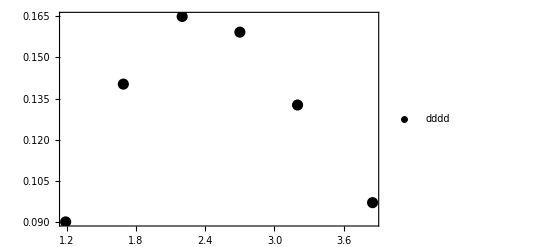

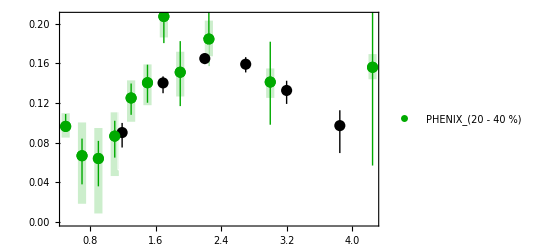

```mathematica
v2P20401=ErrorListPlot[Table[{{v2P2040[[i,1]],v2P2040[[i,2]]},ErrorBar[0.05,{v2P2040[[i,5]],v2P2040[[i,6]]}]},{i,1,Length[v2P2040]}],Frame->True,PlotStyle->{Darker[Green]},PlotRange-> Full,ErrorBarFunction->Function[{coords, errs}, {Opacity[0.2],Rectangle[coords+{errs⟦1,1⟧,errs⟦2,1⟧},coords+{errs⟦1,2⟧,errs⟦2,2⟧}]}]];
v2P20402=ErrorListPlot[Table[{{v2P2040[[i,1]],v2P2040[[i,2]]},ErrorBar[{0,0},{v2P2040[[i,3]],v2P2040[[i,4]]}]},{i,1,Length[v2P2040]}],Frame->True,PlotStyle->{Darker[Green],Thick,PointSize[.02]},PlotRange-> Full];
v2P2040c1=ErrorListPlot[Table[{{v2P2040c[[i,1]],v2P2040c[[i,2]]},ErrorBar[0.05,{v2P2040c[[i,5]],v2P2040c[[i,6]]}]},{i,1,Length[v2P2040c]}],Frame->True,PlotStyle->{EdgeForm[Thick],White},PlotRange-> Full,ErrorBarFunction->Function[{coords, errs}, {Opacity[0.2],Rectangle[coords+{errs⟦1,1⟧,errs⟦2,1⟧},coords+{errs⟦1,2⟧,errs⟦2,2⟧}]}]];
v2P2040c2=ErrorListPlot[Table[{{v2P2040c[[i,1]],v2P2040c[[i,2]]},ErrorBar[{0,0},{v2P2040c[[i,3]],v2P2040c[[i,4]]}]},{i,1,Length[v2P2040c]}],Frame->True,PlotStyle->{Black,Thick,PointSize[.02]},PlotRange-> Full];
Dat=ListPlot[Table[{v2P2040[[i,1]],v2P2040[[i,2]]},{i,1,Length[v2P2040]}],PlotStyle->{Darker[Green],Thick,PointSize[.02]},Frame->True,PlotRange->Full,PlotLegends->Placed[PointLegend[{Style["PHENIX_(20 - 40  %)",24]},LegendMarkers-> {Graphics[{Darker[Green],Rectangle[{0,0},{.05,1}],Disk[{0.025,.5},.3],Black,Rectangle[{0.8,0},{.85,1}],Disk[{0.825,.5},.3]}]},LegendMarkerSize->24],{Left,Top}]];
Datc=ListPlot[Table[{v2P2040c[[i,1]],v2P2040c[[i,2]]},{i,1,Length[v2P2040c]}],PlotStyle->{Black,Thick,PointSize[.02]},Frame->True,PlotRange->Full,PlotLegends->Placed[PointLegend[{Style["dddd",20]},LegendMarkers-> {Graphics[{Darker[Green],Rectangle[{0,0.5},{.05,1.5}],Disk[{0.025,1},.3]}]},LegendMarkerSize->20],{Right,Center}]]
Show[v2P20401,v2P20402,v2P2040c1,v2P2040c2,Dat]
```